```mathematica
sampleRate = 200;
addTime[list_] := MapIndexed[{N[(#2[[1]] - 1) / sampleRate], #1} &, list];
window[list_, windowFunc_] := MapIndexed[windowFunc[(#2[[1]] - 1) / (Length[list] - 1) - 0.5] #1 &, list];
relPowerFourier[list_, windowFunc_] := MapIndexed[
{N[(#2[[1]] - 1) sampleRate / Length[list]], #1} &,
Take[
20 Log10@(#1 / Max[#1] &)@Abs@Fourier[window[list, windowFunc], FourierParameters->{1, -1}],
Ceiling[Length[list] / 2]
] /. Indeterminate -> -Infinity
];
relPowerFourier[list_] := relPowerFourier[list, HammingWindow];
import[filename_] := Transpose[{#1[[2]], #1[[4]]} & /@ Drop[Import[filename], 3]];
```

```mathematica
data = Drop[#1, 40 sampleRate] & /@ import["~/phys2113/lab2/data/93cm-1-extra-separation.tsv"];
truncatedData = Take[#1, 20 sampleRate] & /@ data;
(*ListPlot[addTime /@ truncatedData, PlotRange -> All, Joined -> True, ImageSize->Full]*)
```

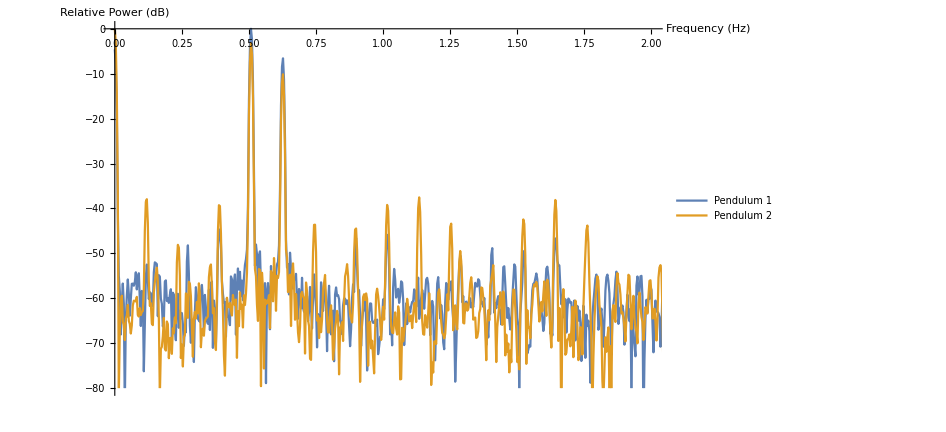

```mathematica
fourierData = ParallelMap[relPowerFourier[#1] &, data];
ListPlot[
fourierData, PlotRange -> {{0, 2}, {-80, 0}},
Joined -> True, PlotMarkers-> None, ImageSize->700,
PlotLegends -> Placed[{"Pendulum 1", "Pendulum 2"}, Above],
AxesLabel -> {"Frequency (Hz)", "Relative Power (dB)"}
]
```